x0= 1

Nmax= 30

epsilon= 0.001

f(x):=Cos[x]

1th iteration value is: 1.64209

estimate error is: 0.

2th iteration value is: 1.57068

estimate error is: 0.

Return[1.5708]

root is: 1.5708

Estimate error is: 0.00012105

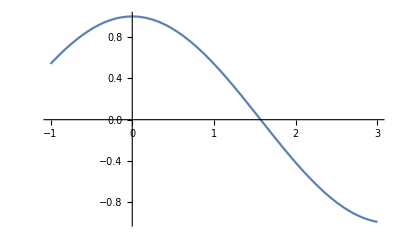

```mathematica
x0=Input["Enter first guess :"];
Nmax=Input["Enter maximum number of iteration :"];
eps=Input["Enter the value of convergence parameter :"];
Print["x0= ",x0];
Print["Nmax= ",Nmax];
Print["epsilon= ",eps];
f[x_]:=Cos[x];
g[x_]:=Dt[f[x],x];
Print["f(x):=",f[x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/.x->x0)/((g[x]/.x->x0))];
If[Abs[x0-x1]<eps,Return[x1],x0=x1;];
Print[i,"th iteration value is: ",x1];
Print["estimate error is: ",Abs[x1-x0]]];
Print["root is: ",x1];
Print["Estimate error is: ",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```

x0= 1

Nmax= 30

epsilon= 0.001

f(x):=Cos[x]-Sin[x]

1th iteration value is: 0.782042

estimate error is: 0.

2th iteration value is: 0.785398

estimate error is: 0.

Return[0.785398]

root is: 0.785398

Estimate error is: 1.26023×10^-8

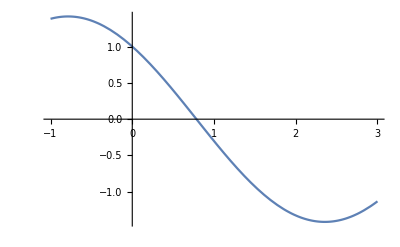

```mathematica
x0=Input["Enter first guess :"];
Nmax=Input["Enter maximum number of iteration :"];
eps=Input["Enter the value of convergence parameter :"];
Print["x0= ",x0];
Print["Nmax= ",Nmax];
Print["epsilon= ",eps];
f[x_]:=Cos[x]-Sin[x];
g[x_]:=Dt[f[x],x];
Print["f(x):=",f[x]];
For[i=1,i≤Nmax,i++,x1=N[x0-(f[x]/.x->x0)/((g[x]/.x->x0))];
If[Abs[x0-x1]<eps,Return[x1],x0=x1;];
Print[i,"th iteration value is: ",x1];
Print["estimate error is: ",Abs[x1-x0]]];
Print["root is: ",x1];
Print["Estimate error is: ",Abs[x1-x0]];
Plot[f[x],{x,-1,3}]
```